```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven4`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Module[
{plot,plotforrange1,plotforrange2,data,size},
data=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}];
size=(Length/@data)//Max;
size=nquestionsUSER;
plot=data//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
plotforrange1=ListLinePlot[{Join[ConstantArray[-dMAX-0.5,size-1],ConstantArray[dMAX+0.5,1]]},ImageSize->Large,TicksStyle->Directive["Label", 20],PlotStyle->None];
Print["size=",size];
Show[plotforrange1,plot]
]

markerphase[in_:GrayLevel[0],out_:GrayLevel[0],size_:7]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Disk[]},PlotRangePadding->0,ImageSize->size]
marker[d_]:=Module[
{DMAX=dMAX,DMIN=-dMAX,opacity=0.08},
d//Which[
#==DMAX,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",470]],ColorData["VisibleSpectrum",470],15*Sqrt[Abs[#]]],
#==DMIN,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",630]],ColorData["VisibleSpectrum",630],15*Sqrt[Abs[#]]],
DMAX>#>0,markerphase[Transparent,ColorData["VisibleSpectrum",470],10*Sqrt[Abs[#]]],
DMIN<#<0,markerphase[Transparent,ColorData["VisibleSpectrum",630],10*Sqrt[Abs[#]]],
#==0,markerphase[Opacity[opacity,Black],Black,10],
True,Style["☒",RGBColor[1, 0, 1],Large]
]&
]


PhasePlot[{biasaffpair_,BeliefFinal_},label_]:=Module[
{meanconclusion,markertable},
meanconclusion=Mean/@BeliefFinal;
markertable=marker/@(meanconclusion);

(List/@biasaffpair)//ListPlot[#,PlotMarkers->markertable,PlotRange->Full,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["b",Bold,Large],Style["a",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&

]

INFO[]:=Module[
{info=""},
info=info<>"dinit = "<>ToString[d]<>"\n";
info=info<>"hinit = "<>ToString[h]<>"\n";
info=info<>"nquestions = "<>ToString[nquestions]<>"\n";
info=info<>"nexperiments = "<>ToString[nexperimentsUSER]<>"\n";
info=info<>"npredictors = "<>ToString[npredictors]<>"\n";
info=info<>"RTHRESHOLD = "<>ToString[RTHRESHOLD]<>"\n";
info=info<>"R0 = "<>ToString[R0]<>"\n";
info=info<>"B0 = "<>ToString[B0]<>"\n";
info=info<>INFOPREDICTIVEPOWER;

info

]


SaveSimulation[id_String]:=Module[
{dir=id,names="",out,PHASE,info=""},
(*saves superarrays*)
(*names=SUPERARRAYNAME//DeleteCases["PLOTS"];
out=(Export[dir<>"/"<>#,#//ToExpression,"String"]&)/@names;
Print/@out;*)
(*saves phase space data*)
PHASE={BiasAffPair,BeliefFinal};
Export[dir<>"/"<>"PHASE",PHASE,"String"];
(*saves BELIEF  data*)
Export[dir<>"/"<>"BELIEF",BELIEF,"String"];
(*saves initital d, h arrays and ranges aMIN,aMAX and bMIN,bMAX, and other values for the simulation.*)
Export[dir<>"/"<>"info",INFO[],"String"];

]
LoadSimulation[id_String]:=Module[
{dir=id,names="",out,pts1,pts2,label},
(*loads superarrays*)
(*names=SUPERARRAYNAME//DeleteCases["PLOTS"]//DeleteCases["EXPERIMENT"];
names={"CREWARD"};
Unprotect/@names;
out=(#<>"=Import[\""<>dir<>"/"<>#<>"\"]//ToExpression"//ToExpression)&/@names;*)
(*loads phase space data*)
PHASE=Import[dir<>"/PHASE"]//ToExpression;
(*loads BELIEF data, WARNING: overrides current value of BELIEF*)
BELIEF//Unprotect;
BELIEF=Import[dir<>"/BELIEF"]//ToExpression;
BELIEF//Protect;
(*prints contents of info file*)
InfoCurrent=Import[dir<>"/info"];Print[InfoCurrent];
(*plot phase diagram*)
pts1=PHASE[[1]]//Length;
pts2=BELIEF//Length;
label=Which[pts1==pts2,id<>": pts = "<>ToString[pts1],True,id<>": pts1 = "<>ToString[pts1]<>",  pts2 = "<>ToString[pts2]];
PhasePlot[PHASE,label]

]

nquestionsUSER=2000;
nexperimentsUSER=500;
npredictorsUSER=20;
(*affinity related settings, keep fixed*)
RTHRESHOLD=4.04;
NSTABLE=4;
R0=50;
(*bias related settings*)
B0=0.7;
(*set forecast: dmax=4,nsteps=8, max power= 21 ⟹ max{Subscript[p, avg]} = 0.9545 , keep fixed *)
BuildPredictivePowerFunction[4,8];

(*unused but needed for function below 'InitSimulationRewardDriven'*)
a=ConstantArray[0,npredictorsUSER];
b=ConstantArray[0,npredictorsUSER];
```

ν values = {1.,1.58824,2.66667,5.28571,21.}

ν values = {1.,1.58824,2.66667,5.28571,21.}

Initialize simulation. 
This sets up the INITIAL values for d,a,b,h which are all lists of size ‘nquestionsUSER’:
- d:  is  the degree of belief on the theory (theory is correct by construction)
- a:  the affinity or tendency for experts to change their belief on the theory, motivated by getting higher rewards.
- b:  is the bias or tendency to reject the objective outcome of experiments, based on their own belief of the theory 
- h:  random walk parameter, associated to the  probability  of experts to change their degree of belief randomly,
          Probability of Random Walk = 2h(1-h)
         examples:  h=0.5   →  50%   ,  h=0.99   →  2% ,  h=1.0   →  0% (no random walk).
The simulation performs a number of experiments given by ‘nexperimentsUSER’. Each experiment asks a number of questions given by  ‘nquestionsUSER’

```mathematica
(*Parameteres to vary. These values are also saved when calling 'SaveSimulation'*)
d={4,3,2,1,0,-1,-2,-3,-4,4,3,2,1,0,-1,-2,-3,-4,0,0};
h=ConstantArray[0.99,npredictorsUSER];
aMIN=1;aMAX=5;(*generate random numbres in this range*)
bMIN=0.0;bMAX=10;(*generate random numbres in this range*)
(*initializes the simulation*)
InitSimulationRewardDriven[d,a,b,h];
```

Run simulation. 
This runs a ‘for-loop’, each iteration corresponds to an experiment. The first iteration uses values set up above for d,a,b,h. 
The degree of belief d is updated according to a,b,h. At the end of every iteration, the values of a,b are changed to be used for the next iteration.
The value of h stays constant during the entire simulation. 
SUPERARRAYS and variable ‘PHASE’ are saved at intermediate steps. 
WARNING: Change the “id” each simulation so that previous work does not get overwritten. Results are   stored in a subdirectory named after the value of  ‘id’.

```mathematica
id="someid";(*change each simulation*) 
tempplot=0;
SaveSimulation[id];
For[it=1,it≤nexperimentsUSER,it++,
(*sets and stores values of a,b for all iterations*)
a=ConstantArray[RandomReal[{aMIN,aMAX}],npredictors];
b=ConstantArray[RandomReal[{bMIN,bMAX}],npredictors];
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*to show progress*)
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperimentStop[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*deletes display of progress *)
NotebookDelete[templine];
(*store values for phase plot*)
BiasAffPair=Table[{BiasValues[[i]],AffinityValues[[i]]},{i,1,AffinityValues//Length}];
BeliefFinal=Table[BELIEF[[i,-1]],{i,1,BELIEF//Length}];
phase=PhasePlot[{BiasAffPair,BeliefFinal},"j="<>ToString[it]];
If[Mod[it,10]==0||it==1,NotebookDelete[tempplot];tempplot=PrintTemporary[phase]];

If[
Mod[it,30]==0,
SaveSimulation[id],
Nothing,Nothing
]

]
EXPERIMENT//Flatten//Cases[x_:>x/;!NumericQ[x]];
Print[Style["This should print a value of 0: value =  ",Large,Bold,Black],Style[%//Length,Bold,Large,Blue]]
SaveSimulation[id]
```

$Aborted

This should print a value of 0: value =  0

Values for phase plot stored in ‘id/PHASE’ and values of BELIEF stored in ‘id/BELIEF’, where ‘id’ is the string defined right before the loop above. Info file stored in ‘id/info’.
Stored simulations can be loaded by calling ‘LoadSimulation[ID]’, with ID a string that should match a previously used value of ‘id’.

dinit = {4, 3, 2, 1, 0, -1, -2, -3, -4, 4, 3, 2, 1, 0, -1, -2, -3, -4, 0, 0}
hinit = {0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99}
nquestions = 2000
nexperiments = 500
npredictors = 20
RTHRESHOLD = 4.04
R0 = 50
B0 = 0.7
######## predictive power function genereted by calling: 'BuildPredictivePowerFunction[4,8]'
dMAX = 4
dSTEPS = 8
dSTEPSIZE = 1
forecastavgMAX = 0.954545
PowerValues = {1., 1.58824, 2.66667, 5.28571, 21.}
forecastavg = {0.0454545, 0.159091, 0.272727, 0.386364, 0.5, 0.613636, 0.727273, 0.840909, 0.954545}

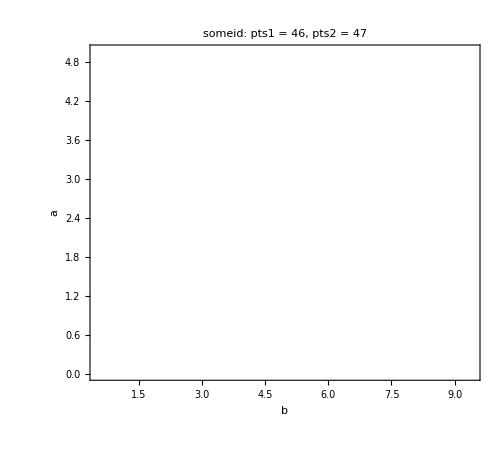

```mathematica
ID="someid";
LoadSimulation[ID]
```